```mathematica
Needs["OpenCLLink`"]
```

```mathematica
workGroupSize = 256;
nBodies=10 * workGroupSize;
radius=1;
dt = 0.1;
epsilon = 0.5;
```

Create Initial Conditions

```mathematica
q0:=RandomReal[{0,100},{nBodies,2}];
p0:=RandomReal[{-4,4},{nBodies,2}];
```

```mathematica
clq=OpenCLMemoryLoad[q0,"Float2"];
clp=OpenCLMemoryLoad[p0,"Float2"];
```

```mathematica
halfStep=OpenCLFunctionLoad["
	__kernel void euler(__global float2 * q, __global float2 * p, float dt, int size) {
	int i = get_global_id(0);
	if(i < size) {
		float2 x = q[i];
		float2 v = p[i];
		//v = v + dt * (float2)(0.0,-10.0);
		x = x + dt * v;
		if(x[0] <= 0.0 && v[0] < 0.0) {
			x[0] = 0.0;
			v[0] = -v[0];
		}
		if(x[0] >= 100.0 && v[0] > 0.0) {
			x[0] = 100.0;
			v[0] = -v[0];
		}
		if(x[1] <= 0.0 && v[1] < 0.0) {
			x[1] = 0.0;
			v[1] = -v[1];
		}
		if(x[1] >= 100.0 && v[1] > 0.0) {
			x[1] = 100.0;
			v[1] = -v[1];
		}
		q[i] = x;
		p[i] = v;
	}
}
","euler",{{"Float2"},{"Float2"},"Float",_Integer},workGroupSize,"Defines"->{"EPS"->epsilon}];
```

```mathematica
csrJor=OpenCLFunctionLoad["
typedef float real_t;
__kernel void csr_jor(__global unsigned int * rows, __global unsigned int * columns, __global real_t * tij, __global real_t * b, __global real_t * la0, __global real_t * la1, __global unsigned int * converged, real_t tol_rel, unsigned int size) {
	unsigned int i = get_global_id(0);
	if(i == 0)
		converged[0] = true;
	if(i < size) {
		__global unsigned int * jptr = columns + rows[i];
		__global unsigned int * jptr_end = columns + rows[i + 1];
		__global real_t * tptr = tij + rows[i];
		
		real_t la = b[i];
		for(;jptr < jptr_end; ++jptr, ++tptr) {
			la = la + (*tptr) * la0[*jptr];
		}
		//prox r^+
		la1[i] = max((real_t)0, la);
		//check convergence criterion
		bool convgd = fabs(la1[i] - la0[i]) <= tol_rel * fabs(la0[i]);
		if(!convgd)
			converged[0] = false;
	}
}","csr_jor",{{"Integer32"},{"Integer32"},{"Float"},{"Float"},{"Float"},{"Float"},{"Integer32"},"Float","Integer32"},workGroupSize];
```

```mathematica
clAllConverged=OpenCLFunctionLoad["
__kernel void all_converged(
  __global unsigned int * converged,
  unsigned int size
) {
	unsigned int i = get_global_id(0);
	if(i < size) {
		if(!converged[i])
			converged[0] = false;
	}
}
","all_converged",{{"Integer32"},"Integer32"},workGroupSize];
```

```mathematica
rows={0,2,5,8,10};
columns={0,1,0,1,2,1,2,3,2,3};
t={0,0.5,0.5,0,0.5,0.5,0,0.5,0.5,0};
b={1,0,0,0};
la0={0,0,0,0};
la1={0,0,0,0};
cvgd={0,0,0,0};
tolrel=10.0^(-6);
```

```mathematica
clr=OpenCLMemoryLoad[rows,"Integer32"];
clc=OpenCLMemoryLoad[columns,"Integer32"];
clt=OpenCLMemoryLoad[t,"Float"];
clb=OpenCLMemoryLoad[b,"Float"];
clla0=OpenCLMemoryLoad[la0,"Float"];
clla1=OpenCLMemoryLoad[la1,"Float"];
clcv=OpenCLMemoryLoad[cvgd,"Integer32"];
```

```mathematica
allConverged[l_]:=Fold[#1&& #2==1&,True,l]
```

```mathematica
Converged[x_,y_,t_]:=Inner[#1<=#2&,Abs[x-y] , t*Abs[x],#1&&#2&]
```

```mathematica
csrJor[clr,clc,clt,clb,clla0,clla1,clcv,1.0,4,4];
```

```mathematica
OpenCLMemoryGet[clcv]
```

{0,0,0,0}

```mathematica
clcv=OpenCLMemoryLoad[{1,1,1,0},"Integer32"];
```

```mathematica
clAllConverged[clcv,4]
```

{OpenCLMemory[<246501672>,Integer32]}

```mathematica
OpenCLMemoryGet[clcv]
```

{0,1,1,0}

66

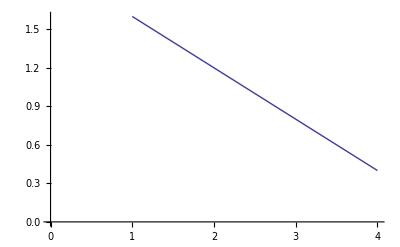

```mathematica
csrJor[clr,clc,clt,clb,clla0,clla1,clcv,tolrel,4,4];
csrJor[clr,clc,clt,clb,clla1,clla0,clcv,tolrel,4,4];
n=2;
While[!OpenCLMemoryGet[clcv][[1]]==1,
csrJor[clr,clc,clt,clb,clla0,clla1,clcv,tolrel,4,4];
csrJor[clr,clc,clt,clb,clla1,clla0,clcv,tolrel,4,4];
n=n+2;
];
n
ListLinePlot[OpenCLMemoryGet[clla0]]
```

66

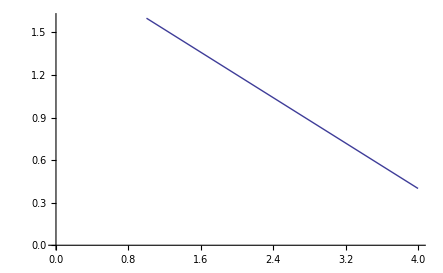

```mathematica
csrJor[clr,clc,clt,clb,clla0,clla1,clcv,tolrel,4,4];
csrJor[clr,clc,clt,clb,clla1,clla0,clcv,tolrel,4,4];
n=2;
While[!allConverged[OpenCLMemoryGet[clcv]],
csrJor[clr,clc,clt,clb,clla0,clla1,clcv,tolrel,4,4];
csrJor[clr,clc,clt,clb,clla1,clla0,clcv,tolrel,4,4];
n=n+2;
];
n
ListLinePlot[OpenCLMemoryGet[clla0]]
```

```mathematica
collide=OpenCLFunctionLoad["
	__kernel void collide(__global float2 * q, __global float2 * p, float dt, int size) {
		int i = get_global_id(0);
		if(i < size) {
			float2 x = q[i];
			float2 v = p[i];
			for(int j = i; j < size; ++j) {
			
			}
		}
}","collide",{{"Float2"},{"Float2"},"Float",_Integer},workGroupSize,"Defines"->{"EPS"->epsilon}];
```

```mathematica
Clear[findCollisions2,findCollisionPairs]
findCollisions2[{_,_,_},{},_]:={}
findCollisions2[{i_,xa_,ya_},{{xb_,yb_},r___},j_]:=With[
{dx=xa-xb,
dy=ya-yb},
If[dx*dx+dy*dy <4*radius*radius,
Prepend[findCollisions2[{i,xa,ya},{r},j+1],{i,j}],
findCollisions2[{i,xa,ya},{r},j+1]]
]
```

```mathematica
findCollisionPairs[{},_]:={}
findCollisionPairs[{{x_,y_},r___},i_]:=Join[findCollisions2[{i,x,y},{r},i+1],findCollisionPairs[{r},i+1]]
```

```mathematica
findCollisionPairs[OpenCLMemoryGet[clq],1]
```

```mathematica
Graphics[{
Hue[0.1],
AbsolutePointSize[radius],
Point[
Dynamic[
Refresh[
halfStep[clq,clp,dt,nBodies,nBodies];
Take[#,2]&/@OpenCLMemoryGet[clq],UpdateInterval->0]]
]
},PlotRange->{{0,100},{0,100}}]
```

```mathematica
randSubdivide[{x_,y_},var_,0]:={x,y}
```

```mathematica
randSubdivide[{x_,y_},var_,n_]:=With[{m=RandomReal[{Max[0,0.5*(x+y)-var],0.5*(x+y)+var}],nvar=var/3},Join[Drop[randSubdivide[{x,m},nvar,n-1],-1],randSubdivide[{m,y},nvar,n-1]]]
```

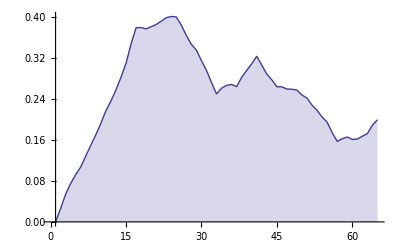

```mathematica
heights=randSubdivide[{0.0,0.2},0.8,6];
ListLinePlot[heights,Filling->Axis,AxesOrigin->{1,0}]
```

```mathematica
nr:=Table[i*1.0/(Length[heights]-1),{i,0,Length[heights]-1}];
```

```mathematica
Length[heights]
```

65

```mathematica
Riffle[nr,heights]
```